# Метод на най-малките квадрати (МНМК)

Задача: (a и b са съответно предпоследната и последната цифра от факултетния номер)
1. Да се състави таблицата (x_k, g(x_k)), където
x_k =  -b + k(0.1), k = OverBar[0,10],   g(x) = ⅇ^(((a+1)x)/10)
Търси се апроксимацията в точката s = -b + (0.17)a + 0.01. За тази цел:
2. Да се построи полином на ленейна регресия по получената таблица.
3. Да се построи полином на квадратична регресия по получената таблица.
4. Да се построи полином на кубична регресия по получената таблица.
5. Да се пресметне апроксимацията, използвайки всеки един от построените полиноми (общо 3).
6. Да се оцени грешката за всяка от получените апроксимации.
7. Да се направи сравнение между трите резултата.

## Генериране на данни

```mathematica
xt = Table[-9+k*0.1, {k, 0, 10}]
```

{-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.}

```mathematica
f[x_] := ⅇ^((2x)/10)
yt = f[xt]
```

{0.165299,0.168638,0.172045,0.17552,0.179066,0.182684,0.186374,0.190139,0.19398,0.197899,0.201897}

```mathematica
P = Length[xt]
```

11

### Визуализация

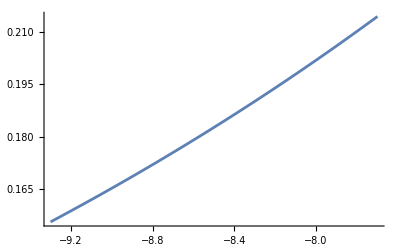

```mathematica
grf = Plot[f[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}]
```

```mathematica
points = Table[{xt[[i]], yt[[i]]}, {i, 1, P}];
```

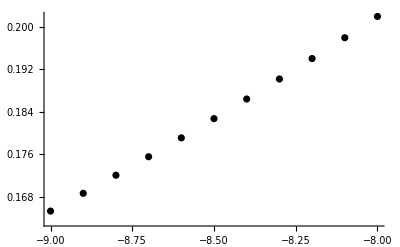

```mathematica
grp = ListPlot[points, PlotStyle->Black]
```

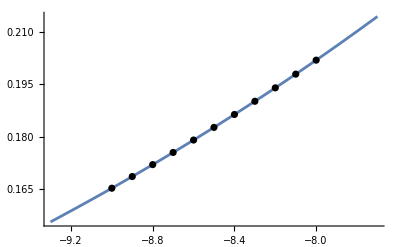

```mathematica
Show[grf, grp]
```

## Линейна регресия

### Попълваме таблицата

```mathematica
xt^2
```

{81.,79.21,77.44,75.69,73.96,72.25,70.56,68.89,67.24,65.61,64.}

```mathematica
yt*xt
```

{-1.48769,-1.50088,-1.51399,-1.52703,-1.53997,-1.55281,-1.56554,-1.57815,-1.59064,-1.60298,-1.61517}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-93.5

```mathematica
∑_(i=1)^P yt[[i]]
```

2.01354

```mathematica
∑_(i=1)^P xt[[i]]^2
```

795.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-17.0749

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]]}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]};
```

```mathematica
LinearSolve[A,b]
```

{0.49398,0.0365801}

### Съставяме полинома

```mathematica
P1[x_] := 0.49398 + 0.0365801x
```

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x}, x]
```

0.49398+0.0365801 x

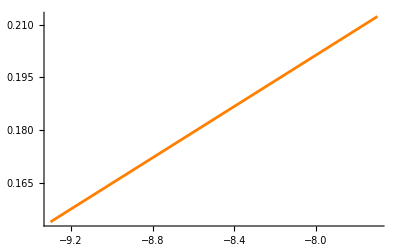

```mathematica
grfP1 = Plot[P1[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle->Orange]
```

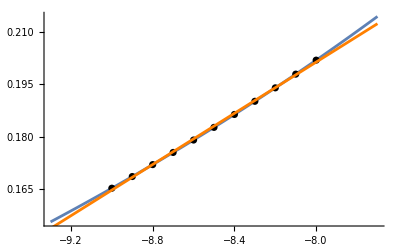

```mathematica
Show[grf, grp, grfP1]
```

```mathematica
P1[-8.25]
```

0.192194

За сравнение истинската стойност

```mathematica
f[-8.25]
```

0.19205

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P1[xt[[i]]])^2)
```

0.00107128

#### Истинска грешка

```mathematica
Abs[f[-5.97] - P1[-5.97]]
```

0.02741

## Квадратична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{81.,79.21,77.44,75.69,73.96,72.25,70.56,68.89,67.24,65.61,64.}

```mathematica
yt*xt
```

{-1.48769,-1.50088,-1.51399,-1.52703,-1.53997,-1.55281,-1.56554,-1.57815,-1.59064,-1.60298,-1.61517}

```mathematica
xt^3
```

{-729.,-704.969,-681.472,-658.503,-636.056,-614.125,-592.704,-571.787,-551.368,-531.441,-512.}

```mathematica
xt^4
```

{6561.,6274.22,5996.95,5728.98,5470.08,5220.06,4978.71,4745.83,4521.22,4304.67,4096.}

```mathematica
yt*xt^2
```

{13.3892,13.3578,13.3232,13.2851,13.2437,13.1989,13.1505,13.0987,13.0432,12.9841,12.9214}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-93.5

```mathematica
∑_(i=1)^P yt[[i]]
```

2.01354

```mathematica
∑_(i=1)^P xt[[i]]^2
```

795.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-17.0749

```mathematica
∑_(i=1)^P xt[[i]]^3
```

-6783.43

```mathematica
∑_(i=1)^P xt[[i]]^4
```

57897.7

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

144.996

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]],  ∑_(i=1)^P yt[[i]]*xt[[i]]^2};
```

```mathematica
LinearSolve[A,b]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{11.,-93.5,795.85},{-93.5,795.85,-6783.43},{795.85,-6783.43,57897.7}} may contain significant numerical errors.

{0.757812,0.0987443,0.00365672}

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x, x^2}, x]
```

0.757812+0.0987443 x+0.00365672 x^2

### Съставяме полинома

```mathematica
P2[x_] := 0.757812 - 0.0987443x + 0.00365672 x^2
```

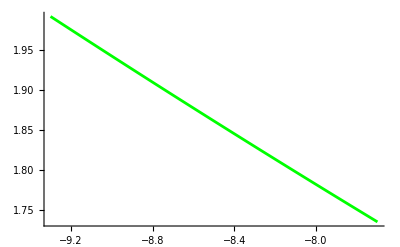

```mathematica
grfP2 = Plot[P2[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle->Green]
```

```mathematica
Show[grf,grp,grfP1, grfP2]
```

-Graphics-

```mathematica
P2[-8.25]
```

1.82134

За сравнение истинската стойност

```mathematica
f[-8.25]
```

0.19205

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P2[xt[[i]]])^2)
```

5.57131

#### Истинска грешка

```mathematica
Abs[f[-8.25] - P2[-8.25]]
```

1.62929

## Кубична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{81.,79.21,77.44,75.69,73.96,72.25,70.56,68.89,67.24,65.61,64.}

```mathematica
yt*xt
```

{-1.48769,-1.50088,-1.51399,-1.52703,-1.53997,-1.55281,-1.56554,-1.57815,-1.59064,-1.60298,-1.61517}

```mathematica
xt^3
```

{-729.,-704.969,-681.472,-658.503,-636.056,-614.125,-592.704,-571.787,-551.368,-531.441,-512.}

```mathematica
xt^4
```

{6561.,6274.22,5996.95,5728.98,5470.08,5220.06,4978.71,4745.83,4521.22,4304.67,4096.}

```mathematica
yt*xt^2
```

{13.3892,13.3578,13.3232,13.2851,13.2437,13.1989,13.1505,13.0987,13.0432,12.9841,12.9214}

```mathematica
yt*xt^3
```

{-120.503,-118.885,-117.244,-115.581,-113.896,-112.191,-110.465,-108.719,-106.954,-105.171,-103.371}

```mathematica
xt^5
```

{-59049.,-55840.6,-52773.2,-49842.1,-47042.7,-44370.5,-41821.2,-39390.4,-37074.,-34867.8,-32768.}

```mathematica
xt^6
```

{531441.,496981.,464404.,433626.,404567.,377150.,351298.,326940.,304007.,282430.,262144.}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-93.5

```mathematica
∑_(i=1)^P yt[[i]]
```

2.01354

```mathematica
∑_(i=1)^P xt[[i]]^2
```

795.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-17.0749

```mathematica
∑_(i=1)^P xt[[i]]^3
```

-6783.43

```mathematica
∑_(i=1)^P xt[[i]]^4
```

57897.7

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

144.996

```mathematica
∑_(i=1)^P xt[[i]]^5
```

-494840.

```mathematica
∑_(i=1)^P xt[[i]]^6
```

4.23499×10^6

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^3
```

-1232.98

### Решаваме системата

```mathematica
A= ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4, ∑_(i=1)^P xt[[i]]^5}, {∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4, ∑_(i=1)^P xt[[i]]^5, ∑_(i=1)^P xt[[i]]^6}}); b = {∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]^2, ∑_(i=1)^P yt[[i]]*xt[[i]]^3};
```

```mathematica
LinearSolve[A,b]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{11.,-93.5,795.85,-6783.43},{-93.5,795.85,-6783.43,57897.7},{795.85,-6783.43,57897.7,-494840.},{-6783.43,57897.7,-494840.,4.23499×10^6}} may contain significant numerical errors.

{0.907126,0.15153,0.0098719,0.000243733}

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x, x^2,x^3}, x]
```

0.907125+0.15153 x+0.00987189 x^2+0.000243732 x^3

### Съставяме полинома

```mathematica
P3[x_] :=0.907125 + 0.15153x + 0.00987189 x^2 + 0.000243732 x^3
```

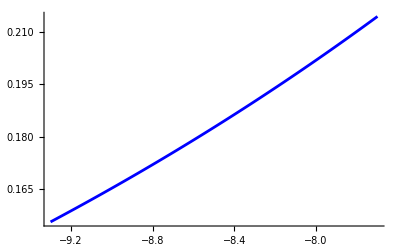

```mathematica
grfP3 = Plot[P3[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle-> Blue]
```

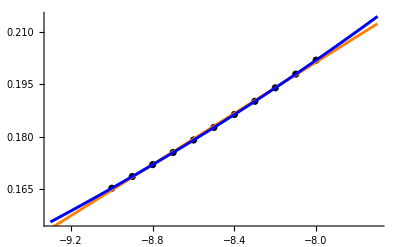

```mathematica
Show[grf, grp, grfP1,grfP2, grfP3]
```

### Намиране на приближена стойност (s = -b + (0.17)a + 0.01)

```mathematica
s = -9 + 0.17  + 0.01
```

-8.82

```mathematica
P3[-8.25]
```

0.192049

За сравнение истинската стойност

```mathematica
f[-8.25]
```

0.19205

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P3[xt[[i]]])^2)
```

4.3115×10^-6

#### Истинска грешка

```mathematica
Abs[f[-8.25] - P3[-8.25]]
```

1.22181×10^-6